# Mathematica 入门 之 符号和数值计算

## 绪论

2021-08-13 陈可鉴

建议配合面向数学学习的快速入门指南https://www.wolfram.com/language/fast-introduction-for-math-students/zh/Nonehttps://www.wolfram.com/language/fast-introduction-for-math-students/zh/HyperlinkActionRecycledHyperlinkActive 食用

通过「高级计算器」来上手

Mathematica 是一款强大的科学计算软件。尽管它有强大的编程能力、优雅的编程逻辑，但是对于我们数学、物理、天文方向的同学来说，最容易上手的还是数学计算。

Mathematica 绝不仅仅是个「高级计算器」，但是我们要先学会把它当做一个「高级计算器」，在日常使用中熟悉 Mathematica 。

符号计算和数值计算

看大纲
本章的内容包括：代数运算、微积分、线性代数、优化、拟合、插值、微分方程、傅里叶分析、概率与统计……

除了拟合、插值和统计是纯粹数值的问题外，其他部分都既可以符号计算（解析计算），又可以数值计算。当解析手段无能为力，或者太过复杂缓慢时，我们就采用数值手段。

MMA 中的数值计算

在多数编程语言中，区分「整型」变量和「浮点型」变量，MMA 与之类似，但有 π 这样的精确数

1 和 1/2 是精确数，1.0 和 0.5 是浮点数（近似数）
π 和 √2是精确数，3.14159 是浮点数

精确数存在于数学中，具有无穷精度
浮点数存在于现实世界的数据中，具有有限精度

## 「精确」代数运算

对于符号输入、精确输入，MMA 不会直接计算成浮点数

```mathematica
Sin[π/17]
```

Sin[π/17]

这为进一步代数计算提供了可能性：

```mathematica
ToRadicals@Sin[π/17]
```

1/4 √(8-√(2 (15+√17-√(2 (17-√17))+√(2 (34+6 √17+√(2 (17-√17))-√(34 (17-√17))+8 √(2 (17+√17)))))))

「上帝公式」

```mathematica
ⅇ^(π ⅈ)
```

-1

## N 用于计算数值

函数 N 可以把精确数计算到任意小数位（当然，越精确越耗时）
为什么是「N」：N for Numeric

```mathematica
N[π,20]
```

3.1415926535897932385

```mathematica
N@{1,3,5,7,9}
```

{1.,3.,5.,7.,9.}

```mathematica
Sin[π/17]//N
```

0.18375

直接使用浮点数进行数值计算：
浮点数和精确数组合，会得到浮点数

```mathematica
2.0*π
```

6.28319

```mathematica
Sin[π/17.]
```

0.18375

一旦计算为浮点数，想还原为精确数就不那么容易了

## N 开头的函数：解析运算的数值版本

```mathematica
Solve->NSolve
Sum->NSum
Integrate->NIntegrate
DSolve->NDSolve
Minimize->NMinimize
Probability->NProbability
```

## 基本数学运算

2021-08-16 陈可鉴

四则运算

## 加减法

```mathematica
a+b-1+4
```

3+a+b

## 乘除法

```mathematica
3*7
```

21

```mathematica
10/5
```

2

```mathematica
3/7
```

3/7

遵从数学习惯：
1. 把数字和符号直接写在一起，视为乘法
2. 把符号和符号用空格隔开，视为乘法

```mathematica
3a+b-2a
```

a+b

```mathematica
a b c
```

a b c

注意写不写空格的区别，a b ≠ ab
这是新手易犯的错误

## 乘方开方

乘方：

```mathematica
a^2
```

a^2

平方根：

```mathematica
Sqrt[2]
```

√2

n 次方根

```mathematica
a^(1/n)
```

a^(1/n)

二维输入

基本思路是在本来要按的键的基础上按住 Ctrl （对于macOS）
详见 菜单栏-插入-排版
也可以打开书写助手面板，但是还是建议用快捷键而非鼠标

```mathematica
{1/3,a^2,√a,Subscript[a, 1]}
```

{1/3,a^2,√a,a_1}

以后讲解到相应函数的时候再讲对应的二维输入

初等函数

幂指对

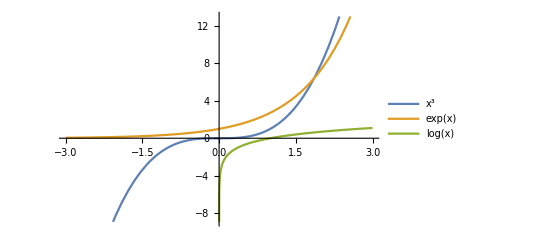

```mathematica
Plot[{x^3,Exp[x],Log[x]},{x,-3,3},PlotLegends->"Expressions"]
```

三角函数

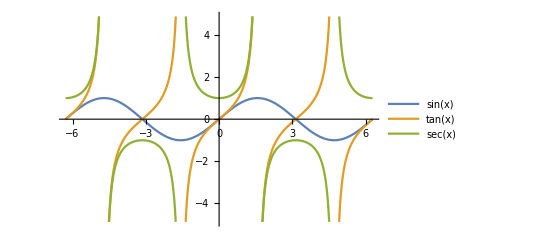

```mathematica
Plot[{Sin[x],Tan[x],Sec[x]},{x,-2π,2π},PlotLegends->"Expressions"]
```

双曲函数

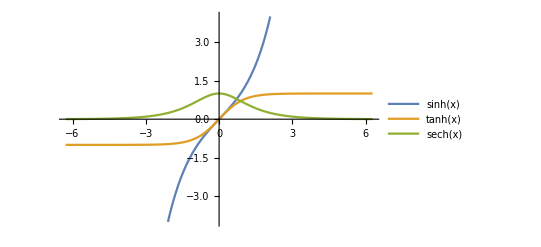

```mathematica
Plot[{Sinh[x],Tanh[x],Sech[x]},{x,-2π,2π},PlotLegends->"Expressions"]
```

反三角函数

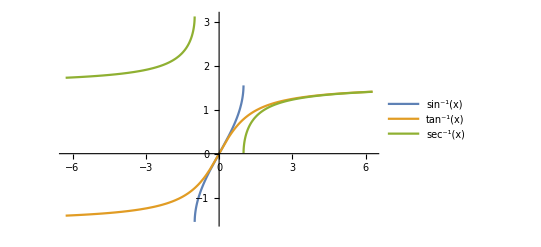

```mathematica
Plot[{ArcSin[x],ArcTan[x],ArcSec[x]},{x,-2π,2π},PlotLegends->"Expressions"]
```

反双曲函数，留做习题

连加 Sum, 连乘 Product, 阶乘 !

## 连加 Sum

```mathematica
1+2+3+4+5
```

15

```mathematica
Sum[i,{i,1,5}]
```

15

Sum 的二维形式
sum  (EscsumEsc)

```mathematica
∑_(i=1)^5 i
```

15

符号计算

```mathematica
∑_(i=1)^n i
```

1/2 n (1+n)

无穷和

```mathematica
∑_(i=1)^∞ 1/i^2
```

π^2/6

```mathematica
∑_(i=1)^∞ 1/i^z
```

Zeta[z]

Sum 还有更多用法，包括跳跃求和、多重求和、不定求和等等，参见帮助文档

## 连乘 Product

```mathematica
Product[Subscript[a, i],{i,1,5}]
```

a_1 a_2 a_3 a_4 a_5

二维形式
prod

```mathematica
∏_(i=1)^∞ (1-1/(4 i^2))
```

2/π

## 阶乘 ! (Factorial)

```mathematica
{10!,10!!}
```

{3628800,3840}

完整形式：实质上是函数「Factorial」

```mathematica
n!//FullForm
```

Factorial[n]

数学函数

参见：
tutorial/MathematicalFunctions

## 数学常数

guide/MathematicalConstants

## 数值函数

这个名字并不恰当，因为这些函数也可以进行符号运算，或许该叫「非解析函数」？
浏览整个数值函数的教程  tutorial/MathematicalFunctions#21826

## 分段函数

```mathematica
Piecewise[{{x^2,x<0},{x,x≥0}}]
```

Piecewise[{{x^2, x<0}, {x, x≥0}, {0, True}}]

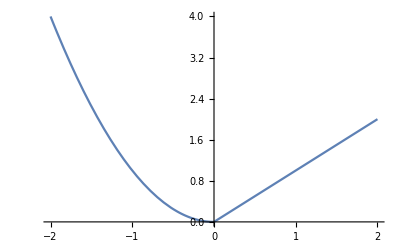

```mathematica
Plot[%,{x,-2,2}]
```

二维输入：pw

```mathematica
Piecewise[{{1, x>0}, {□, □}, {□, □}}]
```

## 整数和数论中的函数

tutorial/MathematicalFunctions#20170

## 特殊函数

guide/SpecialFunctions

## 代数运算

2021-08-24 陈可鉴

以「文档导览」的形式带大家熟悉各个函数。因此本文稿并不全面，请参阅文中给出的帮助文档地址和视频教程。

思维导图：
-Graphics-

逻辑运算

guide/LogicAndBooleanAlgebra

方程和不等式

## 用途？

逻辑分析、判断、假设、区域

```mathematica
Simplify[√(x^2),x<0]
```

-x

## 逻辑约化 Reduce

勾股数 & 费马大定理

```mathematica
Reduce[x^2+y^2==z^2,{x,y,z},Integers]
```

(C[1]|C[2]|C[3])∈ℤ&&C[3]≥0&&((x==C[1] (C[2]^2-C[3]^2)&&y==2 C[1] C[2] C[3]&&z==C[1] (C[2]^2+C[3]^2))||(x==2 C[1] C[2] C[3]&&y==C[1] (C[2]^2-C[3]^2)&&z==C[1] (C[2]^2+C[3]^2)))

```mathematica
Reduce[x^n+y^n==z^n&&n∈Integers&&n>2,{x,y,z},Integers]
```

((n|C[1])∈ℤ&&n≥3&&x==0&&y==C[1]&&z==C[1])||((n|C[1])∈ℤ&&n≥3&&x==C[1]&&y==0&&z==C[1])||((C[1]|C[2])∈ℤ&&C[2]≥2&&n==2 C[2]&&x==0&&y==C[1]&&z==-C[1])||((C[1]|C[2])∈ℤ&&C[2]≥2&&n==2 C[2]&&x==C[1]&&y==0&&z==-C[1])||((C[1]|C[2])∈ℤ&&C[2]≥1&&n==1+2 C[2]&&x==C[1]&&y==-C[1]&&z==0)

```mathematica
Reduce[x^n+y^n==z^n&&n∈Integers&&n>2&&z>y>x>0,{x,y,z},Integers]
```

False

## 寻找例子 FindInstance

公式处理

guide/FormulaManipulation

## 消去变量 Eliminate

```mathematica
Eliminate[{x==Cos[θ],y==Sin[θ]},θ]//Simplify
```

Eliminate::ifun: Eliminate 正在使用反函数，因此可能无法找到某些解；请使用 Reduce 来获取完整的解信息.

x^2+y^2==1

## Thread 用于把等号「逐项作用」于向量

在 基础语法 中还会讲，这里只是先提到

```mathematica
Thread[{a,b,c}=={x,y,z}]
```

{a==x,b==y,c==z}

## 代换：ReplaceAll 和 Rule

方程求解

guide/EquationSolving
tutorial/ManipulatingEquationsAndInequalities

## 求解方程 Solve & NSolve

符号解 & 数值解

## 求根 FindRoot

## 区别 & 联系？

### 符号解：Reduce、Solve、FindInstance

Reduce 是逻辑运算，返回「逻辑表达式」
Solve 求方程的所有解，返回「规则列表」
FindInstance 只找出一个解，返回「规则列表」

```mathematica
Reduce[Sin@x==1,x]
Solve[Sin@x==1,x]
FindInstance[Sin@x==1,x,5]
```

C[1]∈ℤ&&x==π/2+2 π C[1]

{{x→ConditionalExpression[π/2+2 π C[1], C[1]∈ℤ]}}

{{x→-(935 π)/2},{x→-(551 π)/2},{x→(345 π)/2},{x→(685 π)/2},{x→(793 π)/2}}

Reduce 和 Solve 的区别：
Reduce 是逻辑约化，尽可能完整地保留所有信息；Solve 只注重求解，一些特殊情况考虑不到

```mathematica
Reduce[y==k1 x+b1&&y==k2 x +b2,{x,y},Backsubstitution->True]
```

(k1==k2&&b1==b2&&y==b2+k2 x)||(k1-k2≠0&&x==(-b1+b2)/(k1-k2)&&y==(b2 k1-b1 k2)/(k1-k2))

```mathematica
Solve[y==k1 x+b1&&y==k2 x +b2,{x,y}]
```

{{x→-(b1-b2)/(k1-k2),y→-(-b2 k1+b1 k2)/(k1-k2)}}

既然 Solve 能求出所有解，为什么还需要 FindInstance？
看这个例子：

```mathematica
FindInstance[x^2+y^2+z^2==12345678,{x,y,z},Integers]
```

{{x→3338,y→1097,z→5}}

```mathematica
Solve[x^2+y^2+z^2==12345678,{x,y,z},Integers]
```

{{x→-3510,y→-147,z→-63},{x→-3510,y→-147,z→63},{x→-3510,y→-63,z→-147},{x→-3510,y→-63,z→147},{x→-3510,y→63,z→-147},23990,{x→3510,y→-63,z→147},{x→3510,y→63,z→-147},{x→3510,y→63,z→147},{x→3510,y→147,z→-63},{x→3510,y→147,z→63}}
 |  |  |  |

### 数值解：NSolve、FindRoot

NSolve 是 Solve 的数值版本，也是试图求出所有的解。主要处理线性和多项式方程。
FindRoot 用迭代法求根，可以处理很复杂的函数，包括插值函数

```mathematica
Interpolation[{1,3,0,2}][x]
```

InterpolatingFunction[…][x]

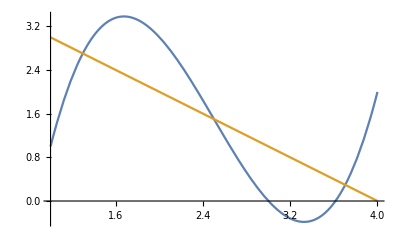

```mathematica
Plot[{Interpolation[{1,3,0,2}][x],4-x},{x,1,4}]
```

```mathematica
FindRoot[Interpolation[{1,3,0,2}][x]==4-x,{x,3}]
```

{x→2.5}

代数运算 习题

推导公式的好习惯：
从各单元间复制粘贴，容易混乱、出错。
如果思路比较清晰，可以直接把各个方程、表达式「命名」，即用 「=」赋值给一个 Symbol。后续用到这些表达式时，直接输入 Symbol 的名字即可。
如果只是作为草稿，可以直接按单元输入，然后用 %xxx 引用单元的输出

## 平抛问题

0. 建立平面直角坐标系，水平方向为 x，竖直方向为 y，存在重力 g (g>0)，忽略阻力。
1. 小球初始位于 {0,0}, 以初始速度 {vx,vy} 抛出，直接写出任意时刻 t 小球的坐标 {x,y} 。
2. 求出小球的轨迹方程（y 和 x 满足的方程），并整理成你看起来最舒服的样子
3. 实际抛射时，更容易控制的是抛出速率 v 和抛射倾角 θ （相对于 x 方向）。将 {vx,vy} 用 v 和 θ 表示，写成规则列表。然后应用这个规则列表，重新表达参数方程和轨迹方程。
4. 设地面位于 y==-h 处，计算抛出的距离。你可能会得到两个解，先不着急区分。
5. 假设参数为 g==10,h==5,v==2,θ==30 度 ，以规则列表的形式写下各组参数。你也可以再自定一组参数。
6. 对于这样的参数，抛出的距离是多少？先计算精确解，然后转换为小数，保留 5 位有效数字。
7. 现在假设地面不是平的，而是服从方程：|x|^3+|y|^3==1，求落点坐标。

1.

```mathematica
eqn={x,y}=={vx,vy}t+1/2{0,-g}t^2
```

{x,y}=={t vx,-(g t^2)/2+t vy}

2.

```mathematica
traj=Eliminate[eqn,t]//FullSimplify
```

g x^2+2 vx^2 y==2 vx vy x

```mathematica
Solve[traj,y]~Collect~x
```

{{y→(vy x)/vx-(g x^2)/(2 vx^2)}}

3.

```mathematica
vRules={vx,vy}==v{Cos@θ,Sin@θ}//ToRules
```

{vx→v Cos[θ],vy→v Sin[θ]}

```mathematica
newtraj=traj/.vRules
```

g x^2+2 v^2 y Cos[θ]^2==2 v^2 x Cos[θ] Sin[θ]

4.

```mathematica
distance=Solve[newtraj/.y->-h,x]//FullSimplify
```

{{x→(v^2 Cos[θ] Sin[θ]-√(v^2 Cos[θ]^2 (2 g h+v^2 Sin[θ]^2)))/g},{x→(v^2 Cos[θ] Sin[θ]+√(v^2 Cos[θ]^2 (2 g h+v^2 Sin[θ]^2)))/g}}

5.

```mathematica
paras1={g->10,h->5,v->2,θ->30Degree};
```

6.

```mathematica
distance/.paras1
```

{{x→1/10 (√3-√303)},{x→1/10 (√3+√303)}}

```mathematica
N[%,5]
```

{{x→-1.5675},{x→1.9139}}

7.

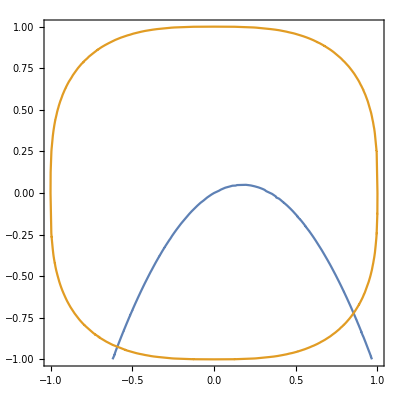

```mathematica
ContourPlot[{newtraj,Abs[x]^3+Abs[y]^3==1}/.paras1//Evaluate,{x,y}∈Rectangle[{-1,-1},{1,1}]]
```

```mathematica
FindRoot[{newtraj,Abs[x]^3+Abs[y]^3==1}/.paras1,{{x,0.01},{y,0}}]
```

{x→0.854011,y→-0.722494}

## 微积分

2021-12-10 陈可鉴

MMA 关于微积分的教程（比较详细）：tutorial/CalculusOverview
MMA 关于微积分的指南（函数导览）：
guide/Calculus

函数属性

导览：
guide/FunctionProperties
配合图像绘制，可以很方便地了解函数的性质

极限 Limit

## 连续极限 Limit

间断点处的极限

```mathematica
Limit[Sin[x]/x,x->0]
```

1

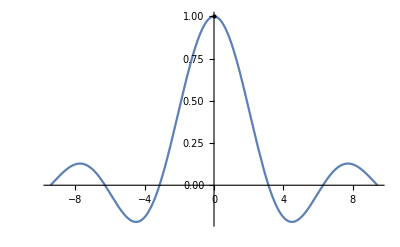

```mathematica
Plot[Sin[x]/x,{x,-3π,3π},Epilog->{PointSize[Large],Point[{0,1}]}]
```

无穷远处的极限：
（∞ 符号：inf）

```mathematica
Limit[Sin[x]/x,x->-∞]
```

0

如果极限不存在，给出 Indeterminate

```mathematica
Limit[Sin[1/x],x->0]
```

Indeterminate

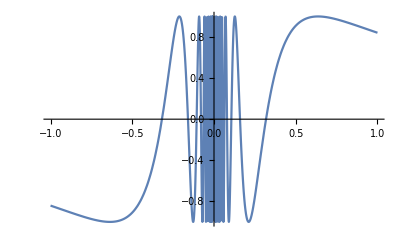

```mathematica
Plot[Sin[1/x],{x,-1,1}]
```

多元函数的极限，请自行参考 Limit 的帮助文档

符号极限：
example：按定义求导

MMA 出于严谨，不会自动假设未知函数的连续性/解析性，因此下式保留其形式而不化简为函数的导数

```mathematica
Limit[(f[x+Δx]-f[x])/Δx,Δx->0]
```

lim_(Δx→0) (-f[x]+f[x+Δx])/Δx

如果代入具体的函数，则 MMA 能正确处理求导

```mathematica
Limit[(f[x+Δx]-f[x])/Δx,Δx->0]/.f->Sin
```

Cos[x]

```mathematica
Limit[(f[x+Δx^2]-f[x-2Δx])/Δx,Δx->0]/.f->Sin
```

2 Cos[x]

## 离散极限（数列极限）DiscreteLimit

```mathematica
DiscreteLimit[(1+1/n)^n,n->∞]
```

ⅇ

```mathematica
DiscreteLimit[(1+n)^(1/n),n->∞]
```

1

数列极限只有在 ∞ 处才有定义：

```mathematica
DiscreteLimit[(1+1/n)^n,n->1]
```

DiscreteLimit::lim: 极限指定无效.

lim_(n→_ℤ 1) (1+1/n)^n

## 应用：演示函数性质

```mathematica
f[x_] := Sin[Tan[x]]
g[x_]:= Cos[x]f[x]
Limit[{f[x],g[x]},x->π/2]
```

{Indeterminate,0}

```mathematica
Manipulate[Plot[{f[x],g[x]},{x,Pi/2-a,Pi/2+a},PlotLegends->{f[x],g[x]},PerformanceGoal->"Quality"],{a,1,0.001},SaveDefinitions->True]
```

求导

## 偏导 D

一元函数求导：

```mathematica
D[x^(x^(x^(x^x))),x]
```

x^(x^(x^(x^x))) (x^(-1+x^(x^x))+x^(x^(x^x)) Log[x] (x^(-1+x^x)+x^(x^x) Log[x] (x^(-1+x)+x^x Log[x] (1+Log[x]))))

高阶导数：

```mathematica
D[Sin[ω t],{t,3}]
```

-ω^3 Cos[t ω]

甚至是任意阶导数的通式：

```mathematica
D[Sin[ω t],{t,n}]
```

ω^n Sin[(n π)/2+t ω]

「符号函数」求导：

```mathematica
D[f[g[x]],x]
```

f'[g[x]] g'[x]

```mathematica
D[f[x,g[x]],x]
```

g'[x] f^(0,1)[x,g[x]]+f^(1,0)[x,g[x]]

注意：求「某一点上的导数」要先求导再代入，否则变成常数求导得 0

```mathematica
D[Sin[1],x]
```

0

```mathematica
D[Sin[x],x]/.x->1
```

Cos[1]

## 全导数/全微分 Dt

在偏导 D 中，像 y 这样没有显含 x 的式子会认为与 x 无关，

```mathematica
D[y,x]
D[y[x],x]
```

0

y'[x]

而全导数则把 y 对 x 的导数也考虑进去。

```mathematica
Dt[x y,x]
```

y+x Dt[y,x]

全微分：

```mathematica
Dt[x y]
```

y Dt[x]+x Dt[y]

## 导数算符 Derivative

之前我们已经见到 f’[x] 这种直观的写法，在 MMA 中，这是 Derivative 的简写：

```mathematica
f'[x]//InputForm
```

Derivative[1][f][x]

解释：f 被看做一个纯函数（不需要作用在 x 上，f 本身就代表了映射）；Derivative[1] 是一个算符，把 f 映射为其导函数Derivative[1][f]，即 f’ ，再作用于自变量 x

Derivative 可以方便地表示抽象的一元导数、多元偏导数：

```mathematica
D[f[x,y],{x,m},{y,2}]
%//InputForm
```

f^(m,2)[x,y]

Derivative[m, 2][f][x, y]

Derivative 在 MMA 中常用于指定微分方程，但也可用于计算

```mathematica
Sin'
```

Cos[#1]&

```mathematica
Sin'[]
```

1

积分 Integrate

## 基本使用

不定积分

```mathematica
Integrate[f[x],x]
```

∫f[x]ⅆx

定积分

```mathematica
Integrate[f[x],{x,a,b}]
```

∫_a^b f[x]ⅆx

example：

```mathematica
Integrate[1/(x^3+1),x]
```

ArcTan[(-1+2 x)/(√3)]/(√3)+1/3 Log[1+x]-1/6 Log[1-x+x^2]

```mathematica
Integrate[1/(x^3+1),{x,0,1}]
```

1/18 (2 √3 π+Log[64])

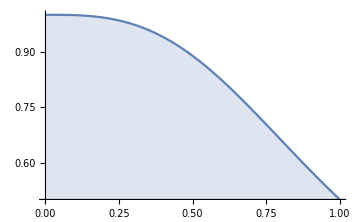

```mathematica
Plot[1/(x^3+1),{x,0,1},Filling->Axis,ImageSize->Medium]
```

## 二维输入

参见 Integrate 的文档

## 区域上的积分

```mathematica
Integrate[x^2+y^4,{x,y}∈Disk[]]
```

(3 π)/8

```mathematica
Plot3D[x^2+y^4,{x,y}∈Disk[],Filling->0,Mesh->None]
```

-Graphics3D-

```mathematica
Integrate[x^2+y^4,{x,y}∈Rectangle[{0,0},{3,4}]]
```

3252/5

## 符号积分

上述已经是符号计算了，但是 MMA 不止于此。Mathematica 的统一性使其可以将微分、积分一起分析：

```mathematica
∂_x ∫_a[x]^b[x] f[t]ⅆt//TraditionalForm
```

f(b(x)) b'(x)-f(a(x)) a'(x)

## 数值积分 NIntegrate

Mathematica 的统一性——数值积分和符号积分的语法几乎没有区别。只需加上 N 函数，使用 N 开头的函数，或者使用近似数。

```mathematica
N@Integrate[1/(x^3+1),{x,0,1}]
NIntegrate[1/(x^3+1),{x,0,1}]
Integrate[1/(x^3+1),{x,0,1.}]
```

0.835649

0.835649

0.835649

更多例子、用法参见 Integrate 和 NIntegrate 的文档

幂级数 Series

幂级数包括 Taylor 级数和 Laurent 级数（复变函数）

## Series 有限项级数

```mathematica
Series[Exp[x],{x,0,10}]
Series[Cos[x],{x,0,10}]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800+O[x]^11

1-x^2/2+x^4/24-x^6/720+x^8/40320-x^10/3628800+O[x]^11

```mathematica
%1*%2
```

1+x-x^3/3-x^4/6-x^5/30+x^7/630+x^8/2520+x^9/22680+O[x]^11

后面的 O[x]表示余项，用 Normal 截断，转换为通常的表达式

```mathematica
Normal@%
```

1+x-x^3/3-x^4/6-x^5/30+x^7/630+x^8/2520+x^9/22680

可视化 Sin 的 Taylor 展开

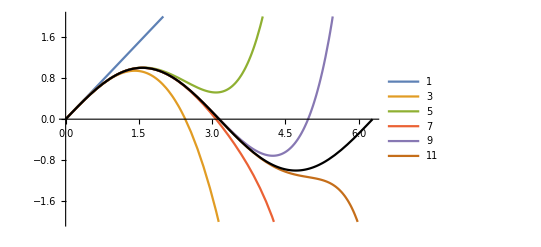

```mathematica
Plot[Sin@x,{x,0,2π},PlotStyle->Directive[Black,Thick]];
Plot[
Table[Normal[Series[Sin[x],{x,0,n}]],{n,1,11,2}]//Evaluate,{x,0,2π},PlotLegends->Range[1,11,2],PlotRange->2];
Show[%,%%]
```

Series 甚至支持未知函数的级数展开
不过不能令展开阶数未知（因为毕竟要给出截断）

```mathematica
Series[f[x] Sin[x]^n,{x,0,3}]
```

x^n (f[0]+f'[0] x+(-1/6 n f[0]+f''[0]/2) x^2+1/6 (-n f'[0]+f^(3)[0]) x^3+O[x]^4)

## SeriesCoefficient 级数的系数

可以用于求级数展开的系数

```mathematica
SeriesCoefficient[Cos[x],{x,0,4}]
```

1/24

甚至可以给出通式（即，令阶数任意）

```mathematica
SeriesCoefficient[Cos[x],{x,0,n}]
```

Piecewise[{{(ⅈ^n (1+(-1)^n))/(2 n!), n≥0}, {0, True}}]

```mathematica
Sum[(ⅈ^n (1+(-1)^n))/(2 n!)x^n,{n,0,∞}]
```

Cos[x]

微积分 习题

从高数书上随便找几道题

## 矢量分析

2022-01-05~2022-01-14
陈可鉴

参见
guide/OperationsOnVectors
guide/VectorAnalysis

内容大纲：
-Graphics-

坐标系之间的转换、任意曲线坐标系的表示、内积外积的推广、张量分析与广义相对论 等内容，留到《Mathematica 进阶——符号和数值计算》中

矢量的表示

「矢量」，粗浅地说，是一个「有大小、方向」的「对象」。

我们常见的「有序实数对」，是「矢量」在某个坐标系下的「表示」。

最常见的表示是在直角坐标系下，这时可以直接加减、点乘。在其他坐标下的运算就比较复杂。

MMA 中默认当然是在直角坐标系下表示矢量，「列表 List」天然具有直角坐标系矢量的含义。但你也可以用列表来存放曲线坐标系的矢量，只是运算不那么直接罢了。

example: 一个 3 维矢量：

```mathematica
{a,b,c}
```

矢量的代数运算

## 矢量的加减、数乘

数学上，矢量空间需要配备两种运算——「加法」和「数乘」

```mathematica
{1,2,3}+{a,b,c}
{1,2,3}-{a,b,c}
3{a,b,c}
{a,b,c}/3
```

{1+a,2+b,3+c}

{1-a,2-b,3-c}

{3 a,3 b,3 c}

{a/3,b/3,c/3}

## 列表运算（实际上不属于矢量运算）

这些是「按元素运算」，不是矢量空间的运算法则。不过用于构造矢量、数据处理等，也挺实用的

```mathematica
{1,2,3}*{a,b,c}
{1,2,3}/{a,b,c}
{1,2,3}^{a,b,c}
{a,b,c}^5
```

{a,2 b,3 c}

{1/a,2/b,3/c}

{1,2^b,3^c}

{a^5,b^5,c^5}

## 点乘、叉乘

点乘的 . 就是英文句号

```mathematica
{1,2,3}.{a,b,c}
Dot[{1,2,3},{a,b,c}]
```

a+2 b+3 c

a+2 b+3 c

叉乘的 × 是 cross

```mathematica
{1,2,3}×{a,b,c}
Cross[{1,2,3},{a,b,c}]
```

{-3 b+2 c,3 a-c,-2 a+b}

{-3 b+2 c,3 a-c,-2 a+b}

交换律 / 反交换律

```mathematica
{1,2,3}.{a,b,c}=={a,b,c}.{1,2,3}
{1,2,3}×{a,b,c}==-{a,b,c}×{1,2,3}
```

True

True

内积空间的操作

数学上，配备了「内积」的矢量空间，成为「内积空间」
有了内积，我们就可以定义向量的模长、夹角、投影、正交等等

## Norm 求模长

```mathematica
Norm@{1,2,3}
Norm@{a,b,c}
Norm[{a,b,c},p]
```

√14

√(Abs[a]^2+Abs[b]^2+Abs[c]^2)

(Abs[a]^p+Abs[b]^p+Abs[c]^p)^(1/p)

## Normalize 归一化

注意与 Normal 区分，Normal 是把表达式转换为普通形式

```mathematica
Normalize@{a,b,c}
```

{a/(√(Abs[a]^2+Abs[b]^2+Abs[c]^2)),b/(√(Abs[a]^2+Abs[b]^2+Abs[c]^2)),c/(√(Abs[a]^2+Abs[b]^2+Abs[c]^2))}

## VectorAngle 向量夹角

```mathematica
VectorAngle[{1,2,3},{2,3,4}]
ArcCos[({1,2,3}.{2,3,4})/(Norm@{1,2,3}*Norm@{2,3,4})]
```

ArcCos[10 √(2/203)]

ArcCos[10 √(2/203)]

对于复向量，需要求共轭

```mathematica
VectorAngle[{1,2,3},{a,b,c}]
ArcCos[({1,2,3}.{a,b,c}*)/(Norm@{1,2,3}*Norm@{a,b,c})]
```

ArcCos[(Conjugate[a]+2 Conjugate[b]+3 Conjugate[c])/(√14 √(Abs[a]^2+Abs[b]^2+Abs[c]^2))]

ArcCos[(Conjugate[a]+2 Conjugate[b]+3 Conjugate[c])/(√14 √(Abs[a]^2+Abs[b]^2+Abs[c]^2))]

## Projection 投影

```mathematica
Projection[{a,b,c},{1,1,1}]
Projection[{1,4,6},{2,3,5}]
```

{1/3 (a+b+c),1/3 (a+b+c),1/3 (a+b+c)}

{44/19,66/19,110/19}

向量微积分

## 求导&积分

### 求导

对参数的求导就是「按元素求导」

```mathematica
D[{a[x],b[x,y],c},x]
```

{a'[x],b^(1,0)[x,y],0}

例子：平抛运动，位移对时间求导=速度

```mathematica
D[{vx t,vy t-1/2 g t^2},t]
```

{vx,-g t+vy}

### 积分

矢量的直接积分：∫ OverVector[A(t)] ⅆt

```mathematica
Integrate[{vx,-g t+vy},t]
```

{t vx,-(g t^2)/2+t vy}

矢量的「第一类曲线/曲面/体积分」，其实就是各分量分别积分，再拼到一起。

```mathematica
Integrate[{-y,x},{x,y}∈Circle[]]
```

{0,0}

### 第二类曲线/曲面积分

矢量的「点乘积分」，即「第二类曲线积分」和「第二类曲面积分」比较麻烦，MMA 中没有一步到位的函数，需要自己稍作变形。下面以第二类曲线积分为例，曲面积分、叉乘积分同理。

我能想到的有 4 种方法。

作为演示，给出一个简单例子：矢量场 {-y,x} 沿单位圆逆时针积分一圈

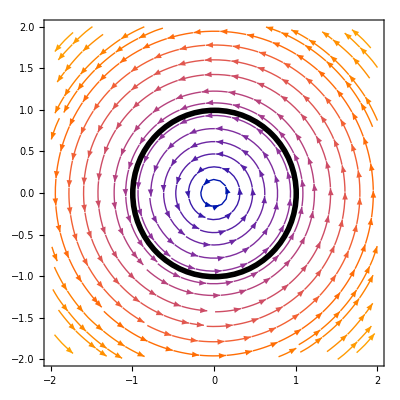

```mathematica
StreamPlot[{-y,x},{x,-2,2},{y,-2,2},Epilog->{Thickness[.01],Circle[]}]
```

#### 拆成坐标分量的积分

∫ A⃗·OverVector[ⅆs] =∫ A_xⅆx+∫ A_yⅆy

```mathematica
Solve[x^2+y^2==1,y]
Solve[x^2+y^2==1,x]
```

{{y→-√(1-x^2)},{y→√(1-x^2)}}

{{x→-√(1-y^2)},{x→√(1-y^2)}}

```mathematica
Integrate[-y/.y->-√(1-x^2),{x,-1,1}]+Integrate[-y/.y->√(1-x^2),{x,1,-1}]+Integrate[x/.x->√(1-y^2),{y,-1,1}]+Integrate[x/.x->-√(1-y^2),{y,1,-1}]
```

2 π

#### 手动给定切向量/法向量，化为第一类积分

∫ OverVector[A(
x⃗)]·OverVector[ⅆs] = ∫ OverVector[A(
x⃗)]· OverHat[s(x⃗)] ⅆs

```mathematica
Integrate[{-y,x}.{-y,x},{x,y}∈Circle[]]
```

2 π

#### 曲线/曲面参数化，化为对参数积分

∫ OverVector[A(
x⃗)]·OverVector[ⅆs] = ∫ OverVector[A(OverVector[x(t)])]·OverVector[(ⅆs(t))/ⅆt]ⅆt

```mathematica
path={Cos@θ,Sin@θ};(*积分路径的参数化，参数为θ*)
tangentVector=D[path,θ](*求路径的切矢*)
substitution=Thread[{x,y}->path](*建立一个 Rule 把直角坐标替换为路径上参数表示的点*)
```

{-Sin[θ],Cos[θ]}

{x→Cos[θ],y→Sin[θ]}

```mathematica
Integrate[({-y,x}/.substitution).tangentVector,{θ,0,2π}]
(*把向量场表达为路径上的值，然后与切矢点乘，再积分*)
```

2 π

#### 使用 Green/Gauss/Stokes 定理

对于闭合曲线/曲面积分比较好用
∮ OverVector[A(
x⃗)]·OverVector[ⅆs] = ∫∫ (∇×A⃗)·OverVector[ⅆS]
∯  OverVector[A(
x⃗)]·OverVector[ⅆS] = ∫∫∫ ∇·A⃗ ⅆV

```mathematica
Integrate[Curl[{-y,x},{x,y}],{x,y}∈Disk[]]
```

2 π

但是，特殊情况下 Green 定理会出错，比如下面这个情况，矢量场的旋度除了原点处处为 0，但在原点处是 δ 函数，MMA 计算旋度的时候忽略了原点处的奇异性

```mathematica
Curl[{-y,x}/(x^2+y^2),{x,y}]//Simplify
```

0

```mathematica
Integrate[Curl[{-y,x}/(x^2+y^2),{x,y}],{x,y}∈Disk[]]
```

0

用其他方法算出来是对的

```mathematica
Integrate[({-y,x}/(x^2+y^2)).{-y,x},{x,y}∈Circle[]]
```

2 π

## 矢量微分算符

这些函数默认在直角坐标下进行计算，输入第三个参数可以指定坐标系。
第三个参数的可选项是 MMA 内置支持的许多坐标系，完整列表可通过 CoordinateChartData[] 获得

常用的有：
直角坐标 “Cartesian”
极坐标 “Polar”
柱坐标 “Cylindrical”
球坐标 “Spherical”

注：有没有觉得直角坐标的名字怪怪的？实际上这是「笛卡尔坐标系」，笛卡尔英文是 Descartes，拉丁文 Cartesius

### 梯度 Grad

```mathematica
Grad[f[x,y,z],{x,y,z}]
```

{f^(1,0,0)[x,y,z],f^(0,1,0)[x,y,z],f^(0,0,1)[x,y,z]}

```mathematica
Grad[x+y,{x,y}]
```

{1,1}

```mathematica
Grad[f[r,θ],{r,θ},"Polar"]
```

{f^(1,0)[r,θ],(f^(0,1)[r,θ])/r}

### 散度 Div

```mathematica
Div[{f[x,y],g[x,y]},{x,y}]
```

g^(0,1)[x,y]+f^(1,0)[x,y]

```mathematica
Div[{-y,x},{x,y}]
```

0

```mathematica
Div[{ρ,0,0},{ρ,ϕ,z},"Cylindrical"]
```

2

### 旋度 Curl

```mathematica
Curl[{f[x,y],g[x,y]},{x,y}]
```

-f^(0,1)[x,y]+g^(1,0)[x,y]

```mathematica
Curl[{f[x,y,z],g[x,y,z],h[x,y,z]},{x,y,z}]
```

{-g^(0,0,1)[x,y,z]+h^(0,1,0)[x,y,z],f^(0,0,1)[x,y,z]-h^(1,0,0)[x,y,z],-f^(0,1,0)[x,y,z]+g^(1,0,0)[x,y,z]}

```mathematica
Curl[{-y,x},{x,y},"Cartesian"]
```

2

### 拉普拉斯算子 Laplacian

标量 Laplacian 是梯度的散度

```mathematica
Laplacian[f[x,y],{x,y}]
```

f^(0,2)[x,y]+f^(2,0)[x,y]

```mathematica
Laplacian[1/r,{r,θ,ϕ},"Spherical"]
```

0

向量场的拉普拉斯算子等于 grad div v+ (-1)^n curl curl v 
（n 是空间维数 ）

注意：矢量 Laplacian 一般来说并不同于 每个分量的标量 Laplacian 的组合！！！只有直角坐标下才恰好相等。

```mathematica
Laplacian[{f[r,θ],g[r,θ]},{r,θ},"Polar"]
Laplacian[#,{r,θ},"Polar"]&/@{f[r,θ],g[r,θ]}
```

{(-(f[r,θ]+g^(0,1)[r,θ])/r+(-g^(0,1)[r,θ]+f^(0,2)[r,θ])/r+f^(1,0)[r,θ])/r+f^(2,0)[r,θ],((-g[r,θ]+f^(0,1)[r,θ])/r+(f^(0,1)[r,θ]+g^(0,2)[r,θ])/r+g^(1,0)[r,θ])/r+g^(2,0)[r,θ]}

{((f^(0,2)[r,θ])/r+f^(1,0)[r,θ])/r+f^(2,0)[r,θ],((g^(0,2)[r,θ])/r+g^(1,0)[r,θ])/r+g^(2,0)[r,θ]}

## 优化

2022-02-05
陈可鉴

参见：
guide/Optimization 
tutorial/ConstrainedOptimizationOverview
tutorial/UnconstrainedOptimizationOverview
（后两篇为深入的专著，初学者不必深究）
（建议使用 12.2 及以后的版本，凸优化方面做了很多更新）

思维导图
-Graphics-

什么是优化问题？

优化问题（Optimization）是非常重要的一大类问题。除了直接的优化问题，许多问题都可以被转化为优化问题，例如：求稳定点、数据拟合、方程数值求根、微分方程数值解、图像降噪、训练神经网络……

在物理题中，我们常常将问题转化为求解代数方程、微分方程。典型的物理问题的范式是「建立模型-求解模型」。

但在实际问题中，人们往往要设计工具、制定策略，这些问题是在寻找「最优解」。这类问题的范式是「建立模型-求解模型-结果最优化」。

在 PT 中，第一类问题居多，前者提法如「解释这一现象并研究相关参数的影响」，后者提法如「优化你的装置以xxx」。
在数学建模竞赛中，基本全都是「优化」问题。

优化问题的数学表述

-Graphics3D-
数学上的优化问题可以写作 min _(x_i∈Reg) f(x_i)
f 是一个标量函数，即「目标函数」
x_i 是一组数，作为「自变量」
Reg 是 x_i 这些数可取的区域，相当于约束关系（等式、不等式、整数…）
最终得到的结果，应该是「最优点」和「最优值」。
（min 和 max 只差一个负号，这里统一用 min 来描述问题。后续的函数也都是 Min 和 Max 对称的）

目标函数是自己选取的。简单的例子如：
拟合：残差的平方和
测量手段：误差
装置发明：功率
商业策略：利润（的相反数）
有多个目标的时候，可以加权相加（当然也有其他方法）

优化问题的分类

符号/数值
局部/全局
约束/非约束

特殊类型：线性规划、凸优化、几何优化、整数规划、图上的优化……

符号优化

## Minimize （全局）最小化

一元函数的非约束最小值
（列表第一个是函数值，第二个是自变量的取值 Rule）

```mathematica
Minimize[2x^2-3x+5,x]
```

{31/8,{x→3/4}}

一元函数的约束最小值

```mathematica
Minimize[{2x^2-3x+5,x≤0},x]
```

{5,{x→0}}

多元函数、带约束的最小值

```mathematica
Minimize[{x-2y,x^2+y^2≤1},{x,y}]
```

{-√5,{x→-1/(√5),y→2/(√5)}}

在几何区域上最优化

```mathematica
minsol=Minimize[x-2y,{x,y}∈Disk[]]
```

{-√5,{x→-1/(√5),y→2/(√5)}}

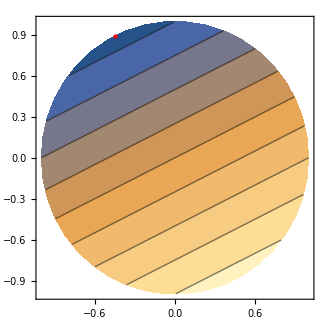

```mathematica
Show[ContourPlot[x-2y,{x,y}∈Disk[]],Graphics[{Red,PointSize[Large],Point[{x,y}/.Last[minsol]]}]]
```

含参数的符号优化

```mathematica
Minimize[a x^2+b x+c,x]
```

{Piecewise[{{c, (b==0&&a==0)||(b==0&&a>0)}, {(-b^2+4 a c)/(4 a), (b>0&&a>0)||(b<0&&a>0)}, {-∞, True}}],{x→Piecewise[{{-b/(2 a), (b>0&&a>0)||(b<0&&a>0)}, {0, (b==0&&a==0)||(b==0&&a>0)}, {Indeterminate, True}}]}}

## MinValue 最小值、ArgMin 最小点

```mathematica
Minimize[2x^2-3x+5,x]
MinValue[2x^2-3x+5,x]
ArgMin[2x^2-3x+5,x]
```

{31/8,{x→3/4}}

31/8

3/4

数值优化

## FindMinimum 数值局部最小化

局部最小化需要指定一个起始点

```mathematica
res=FindMinimum[x Cos[x],{x,2}]
```

{-3.28837,{x→3.42562}}

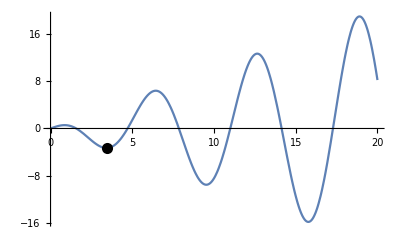

```mathematica
Plot[x Cos[x],{x,0,20},
Epilog->{PointSize[.02],Point[{x/.Last@res,First@res}]}]
```

同样可用于高维的、含约束的局部优化问题。
这里展示一个神奇的例子，来自帮助文档：

求最小的 r 使得三角形和椭圆形仍然交叠：

```mathematica
Subscript[ℛ, 1]=Triangle[{{0,0},{1,0},{0,1}}];
Subscript[ℛ, 2]=Disk[{1,1},{2r,r}];
```

```mathematica
Manipulate[
Graphics[{LightBlue,EdgeForm[Thick],Triangle[{{0,0},{1,0},{0,1}}],Disk[{1,1},{2 r,r}]}]
,
{r,.6,.3}]
```

注意这里的约束指定很巧妙

```mathematica
res=FindMinimum[{r,{x,y}∈Subscript[ℛ, 1]&&{x,y}∈Subscript[ℛ, 2]},{r,x,y}]
```

{0.447214,{r→0.447214,x→0.2,y→0.8}}

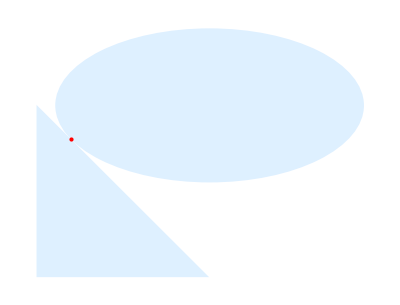

```mathematica
Graphics[{{LightBlue,Subscript[ℛ, 1],Subscript[ℛ, 2]},
{Red,PointSize[Large],Point[{x,y}]}}/.Last[res]]
```

更神奇的是，这个问题其实可以符号计算给出精确解，大家可以自己试一试。

## NMinimize 数值全局最小化

把 Minimize 前面加个 N 就行了，语法几乎一样
NMinValue、NArgMin 同理

```mathematica
NMinimize[2x^2-3x+5,x]
Minimize[2x^2-3x+5.,x]
```

{3.875,{x→0.75}}

{3.875,{x→0.75}}

一个复杂的例子：非线性函数、非线性约束、区域上的优化

```mathematica
func[x_,y_]:=Exp[-y^2] Sin[x^2+y];
cons={Sin[2x]+Cos[3y]≤1,Norm[{x^2,y}]≤2};
reg=Disk[{0,0},2];
res=NMinimize[{func[x,y],cons},{x,y}∈reg]
```

{-0.396653,{x→1.91954×10^-11,y→-0.653271}}

```mathematica
Show[
Plot3D[func[x,y],{x,y}∈reg,
MeshFunctions->{#3&},RegionFunction->Function[{x,y},Sin[2 x]+Cos[3 y]≤1&&Norm[{x^2,y}]≤2],PlotRange->All,PlotPoints->100],Graphics3D[{Blue,PointSize[0.05],Point[{x,y,func[x,y]}/.res⟦2⟧]}]]
```

-Graphics3D-

特殊类型的优化

线性规划：LinearProgramming（矩阵形式）、LinearOptimization（一般形式）
凸优化：ConvexOptimization 等一系列函数
背包问题（0-1 规划）：KnapsackSolve
最短折线路径：FindShortestTour
参见 guide/Optimization

图上的优化：FindMaximumFlow、FindMinimumCostFlow

优化算法漫谈

MMA 的好处就在于，初学者不用管底层的算法，不用把问题分门别类、整理成标准的形式，而可以直接以最接近数学表述的方式，直接求解问题。

不过当需要进一步深入时，有必要了解一些算法的逻辑，有助于你选择合适的算法。

## 符号优化

局部优化（驻点）：梯度为 0
全局优化：在所有驻点和边界点中找最小的那个
约束优化：拉格朗日乘子法
当然，实际上 MMA 用的是一套复杂的计算机代数方法。

## 数值优化

线性/非线性，凸/非凸
局部/全局，约束/非约束，梯度/无梯度，……

局部优化：
	约束问题：内点法、罚函数……
	非约束问题：
		梯度算法：符号计算/手动给出/有限差分近似梯度
			梯度下降、牛顿法、拟牛顿法……
		无梯度算法：主轴法、……

全局优化：
	调用局部优化
	网格法、蒙特卡洛法、进化算法、蚁群算法、模拟退火、贝叶斯优化……

-Graphics3D-

## 拟合

2022-02-11
陈可鉴

参见：
tutorial/NumericalOperationsOnData#19037
guide/CurveFittingAndApproximateFunctions
guide/StatisticalModelAnalysis

-Graphics-

拟合问题简介

## 什么是拟合？

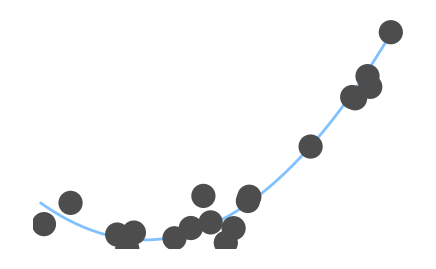
-Graphics--Graphics3D-

我拿到一组数据，认为这组数据背后有一个「规律」，想找出这个函数关系。

但是，我知道这些数据不是精确的，应该是在函数关系的基础上有一定误差。我希望能「把握主干」，找到背后那个简洁的函数。

猜测一个函数形式，调整参数，使得函数给出的「拟合值」总体上与数据尽量「接近」。

注意：完全精确是做不到的，因为数据有误差。

## 具体而言

数据：n 个自变量的值+1 个因变量的值 构成一个数据点。共有若干个数据点。（这里不讨论多个因变量的联合拟合）

拟合函数：自己给定一个函数形式，其中含有若干可变参数，但不能含有未知函数。不一定非要写成显式，也可以是积分、复杂模型的解甚至黑箱函数。
此外，还可以对参数的取值范围进行限制。

「接近」：需要定义一个 NormFunction。常用的是「最小二乘法」，即取 NormFunction 为残差的平方和。

## 把拟合转化为优化问题

从上可见，给定数据和函数形式后，问题就转化为：调整参数值，最小化 NormFunction 。这就归结为一个优化问题。因此，拟合的算法往往归结为优化算法。

注意：优化问题中的变量是拟合函数的「参数」而非「自变量」。

简单拟合函数

## 非线性（一般）拟合：FindFit

对前 20 个质数拟合

没有给定自变量的值，默认是从 1 开始的正整数序列。

```mathematica
data=Prime/@Range@20
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71}

FindFit 返回最优拟合参数的「规则列表」：

```mathematica
FindFit[data,a x Log[b+c x],{a,b,c},x]
```

{a→1.42076,b→1.65558,c→0.534645}

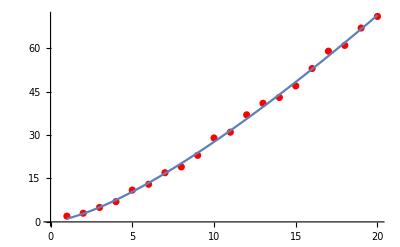

```mathematica
Show[ListPlot[data,PlotStyle->Red],
Plot[a x Log[b+c x]/.{a->1.4207557132167097,b->1.6555813610806136,c->0.5346453246446993},{x,1,20}]]
```

不规则数据，二元拟合：

构建拟合函数，这里显明地把参数和自变量区分开了

```mathematica
Clear@model
model[a_,b_,x0_,y0_][{x_,y_}]:=a Exp[-b((x-x0)^2+(y-y0)^2)];
```

在单位圆内随机取点，构建数据

```mathematica
pointlist=RandomPoint[Disk[],100];
data=Table[
Append[point,model[1.2,5,.3,-.2][point]+RandomReal[{-.1,.1}]],
{point,pointlist}];
```

```mathematica
ListPointPlot3D[data,PlotRange->All]
```

-Graphics3D-

拟合并绘制

```mathematica
fitparas=FindFit[data,model[a,b,x0,y0][{x,y}],{a,b,x0,y0},{x,y}]
```

{a→1.26301,b→5.26884,x0→0.295612,y0→-0.208584}

```mathematica
Show[
ListPointPlot3D[data,PlotRange->All],
Plot3D[model[a,b,x0,y0][{x,y}]/.fitparas,{x,y}∈Disk[]]
]
```

-Graphics3D-

## 线性拟合：Fit

如果拟合函数可以写成一系列（不含参）函数的线性组合，即 f = a_1 f_1+a_2 f_2+...+a_n f_n，那么称这是一个线性拟合。注意：这里的「线性」是指拟合函数对于参数是线性的，不要求对于自变量是线性的。

例如：ax^2+bx+c 虽然关于 x 不是线性的，但关于参数{a,b,c}是线性的。

根据线性代数的理论，线性拟合可以直接算得结果，无需迭代。因此有专门的函数进行处理：Fit。我将来会单写一篇文章讲述其具体原理和几何直观。

```mathematica
data=With[{a=2,b=3.3,c=0.1},Table[{x,a x^2+b x+c},{x,0,10}]]
```

{{0,0.1},{1,5.4},{2,14.7},{3,28.},{4,45.3},{5,66.6},{6,91.9},{7,121.2},{8,154.5},{9,191.8},{10,233.1}}

```mathematica
Fit[data,{1,x,x^2},x]
```

0.1+3.3 x+2. x^2

提取更多拟合信息

## LinearModelFit & NonlinearModelFit

LinearModelFit 语法与 Fit 完全一致
NonlinearModelFit 语法与 FindFit 完全一致
它们返回一个 FittedModel 对象，可以从 FittedModel 中提取各种属性。

## FittedModel

例如，用 NonlinearModelFit 构建一个 FittedModel：

```mathematica
data=Prime/@Range@20;
fittedmodel=NonlinearModelFit[data,a x Log[b+c x],{a,b,c},x]
```

FittedModel[1.42076 x Log[1.65558+0.534645 x]]

首先，它可以当做普通的函数使用：

```mathematica
{fittedmodel[2],fittedmodel@x}
```

{2.84839,1.42076 x Log[1.65558+0.534645 x]}

```mathematica
Show[ListPlot[data,PlotStyle->Red],Plot[fittedmodel@x,{x,1,20}]]
```

-Graphics-

输入特定的字符串（「关键字」），可以提取对应的属性：

```mathematica
fittedmodel["BestFit"]
fittedmodel["BestFitParameters"]
fittedmodel["Data"]
fittedmodel["AdjustedRSquared"]
fittedmodel["ParameterTable"]
```

1.42076 x Log[1.65558+0.534645 x]

{a→1.42076,b→1.65558,c→0.534645}

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71}

0.99935

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.42076 | 0.325437 | 4.36568 | 0.000421097
b | 1.65558 | 0.569912 | 2.90498 | 0.00985807
c | 0.534645 | 0.371929 | 1.43749 | 0.16873

怎么找到有哪些可用的属性？有三种方法：
1. 看提示栏（不完整）
2. 看产生这个 FittedModel 的函数（比如 NonlinearModelFit）的帮助文档的「更多信息和选项」一节
3. 使用 model[“Properties”]

```mathematica
fittedmodel["Properties"]
```

{AdjustedRSquared,AIC,AICc,ANOVATable,ANOVATableDegreesOfFreedom,ANOVATableEntries,ANOVATableMeanSquares,ANOVATableSumsOfSquares,BestFit,BestFitParameters,BIC,CorrelationMatrix,CovarianceMatrix,CurvatureConfidenceRegion,Data,EstimatedVariance,FitCurvatureTable,FitCurvatureTableEntries,FitResiduals,Function,HatDiagonal,MaxIntrinsicCurvature,MaxParameterEffectsCurvature,MeanPredictionBands,MeanPredictionConfidenceIntervals,MeanPredictionConfidenceIntervalTable,MeanPredictionConfidenceIntervalTableEntries,MeanPredictionErrors,ParameterBias,ParameterConfidenceIntervals,ParameterConfidenceIntervalTable,ParameterConfidenceIntervalTableEntries,ParameterConfidenceRegion,ParameterErrors,ParameterPValues,ParameterTable,ParameterTableEntries,ParameterTStatistics,PredictedResponse,Properties,Response,RSquared,SingleDeletionVariances,SinglePredictionBands,SinglePredictionConfidenceIntervals,SinglePredictionConfidenceIntervalTable,SinglePredictionConfidenceIntervalTableEntries,SinglePredictionErrors,StandardizedResiduals,StudentizedResiduals}

拟合技巧

## 把非线性转化为线性

某些特殊的非线性拟合可以转化为线性拟合，大大提升拟合准确度、速度。

例如：
幂函数 f = ax^by^c ，可以取对数变成Log(f)=Log(a)+b Log(x)+c Log(y)
三角函数 f = sin(t+ϕ) 可以展开为 
f = sin(ϕ)cos(t) + cos(ϕ)sin(t)

## 拟合不上怎么办？

非线性拟合可以看作优化问题，拟合不上常常是因为参数较多、参数的初值太偏，落入了局部极小。
可以给定合适的初值，也可以限定参数的范围。
私人秘诀：还可以利用 MMA 强大的交互功能，手动调参到差不多的范围，然后以此作为初值自动拟合

```mathematica
Clear@model
model[a_,ω_,ϕ_,σ_,t0_][t_]:=a Sin[ω t+ϕ]Exp[-((t-t0)/σ)^2]
```

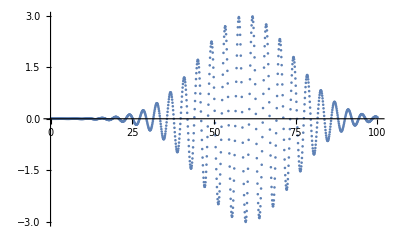

```mathematica
data=Table[{t,model[3,1.5,π,20,60][t]},{t,0,100,.1}];
ListPlot[data,PlotRange->All]
```

```mathematica
fittedmodel=NonlinearModelFit[data,model[a,ω,ϕ,σ,t0][t],{a,ω,ϕ,σ,t0},t]
```

NonlinearModelFit::cvmit: 无法在 100 次迭代中收敛到要求的准确度或者精度.

FittedModel[0.00964051 ⅇ^(-«20» («1»)^2) Sin[0.0146323-1.49611 t]]

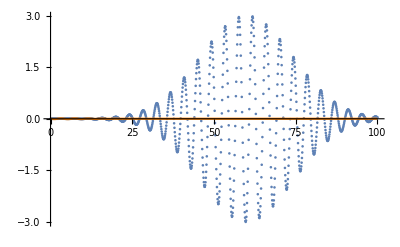

```mathematica
Show[
ListPlot[data,PlotRange->All],Plot[fittedmodel[t],{t,0,100},PlotRange->All,PlotStyle->Orange]
]
```

```mathematica
Manipulate[
Show[
ListPlot[data,PlotRange->All],
Plot[model[a,ω,ϕ,σ,t0][t],{t,0,100},PlotRange->All,PlotStyle->Orange]//Quiet
]
,{a,0,10},{ω,0,10},{ϕ,0,2π},{σ,1,100},{t0,0,100}]
```

ListPlot::lpn: data 不是由数字或者数对组成的列表.

Show::gcomb: 无法合并 Show[ListPlot[data,PlotRange→All],] 中的图形对象.

ListPlot::lpn: data 不是由数字或者数对组成的列表.

Show::gcomb: 无法合并 Show[ListPlot[data,PlotRange→All],] 中的图形对象.

ListPlot::lpn: data 不是由数字或者数对组成的列表.

Show::gcomb: 无法合并 Show[ListPlot[data,PlotRange→All],] 中的图形对象.

ListPlot::lpn: data 不是由数字或者数对组成的列表.

Show::gcomb: 无法合并 Show[ListPlot[data,PlotRange→All],] 中的图形对象.

ListPlot::lpn: data 不是由数字或者数对组成的列表.

Show::gcomb: 无法合并 Show[ListPlot[data,PlotRange→All],] 中的图形对象.

ListPlot::lpn: data 不是由数字或者数对组成的列表.

Show::gcomb: 无法合并 Show[ListPlot[data,PlotRange→All],] 中的图形对象.

ListPlot::lpn: data 不是由数字或者数对组成的列表.

Show::gcomb: 无法合并 Show[ListPlot[data,PlotRange→All],] 中的图形对象.

ListPlot::lpn: data 不是由数字或者数对组成的列表.

Show::gcomb: 无法合并 Show[ListPlot[data,PlotRange→All],] 中的图形对象.

ListPlot::lpn: data 不是由数字或者数对组成的列表.

Show::gcomb: 无法合并 Show[ListPlot[data,PlotRange→All],] 中的图形对象.

ListPlot::lpn: data 不是由数字或者数对组成的列表.

Show::gcomb: 无法合并 Show[ListPlot[data,PlotRange→All],] 中的图形对象.

ListPlot::lpn: data 不是由数字或者数对组成的列表.

Show::gcomb: 无法合并 Show[ListPlot[data,PlotRange→All],] 中的图形对象.

ListPlot::lpn: data 不是由数字或者数对组成的列表.

Show::gcomb: 无法合并 Show[ListPlot[data,PlotRange→All],] 中的图形对象.

ListPlot::lpn: data 不是由数字或者数对组成的列表.

Show::gcomb: 无法合并 Show[ListPlot[data,PlotRange→All],] 中的图形对象.

ListPlot::lpn: data 不是由数字或者数对组成的列表.

Show::gcomb: 无法合并 Show[ListPlot[data,PlotRange→All],] 中的图形对象.

```mathematica
fittedmodel=NonlinearModelFit[data,{model[a,ω,ϕ,σ,t0][t],a>1},{a,ω,ϕ,σ,{t0,50}},t]
```

FittedModel[-3. ⅇ^(-«20» («1»)^2) Sin[21.9911-1.5 t]]

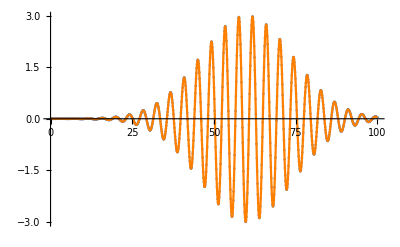

```mathematica
Show[
ListPlot[data,PlotRange->All],Plot[fittedmodel[t],{t,0,100},PlotRange->All,PlotStyle->Orange]
]
```

## 插值

2022-02-14
陈可鉴

参见：
tutorial/NumericalOperationsOnData#24050
guide/CurveFittingAndApproximateFunctions

-Graphics-

什么是插值？

插值，粗略地说，就是画一条曲线，把给定数据点连接起来。

进一步还可以要求在给定点具有给定的导数值。

## 插值与拟合的异同：

拟合：
	认为数据带有误差，不要求经过每个点
	需要人工给定拟合函数的形式
	关注背后简洁的函数关系
插值：
	认为数据误差很小，必须经过每个点
	无需给定函数形式
	不关心函数形式，只要方便计算即可。

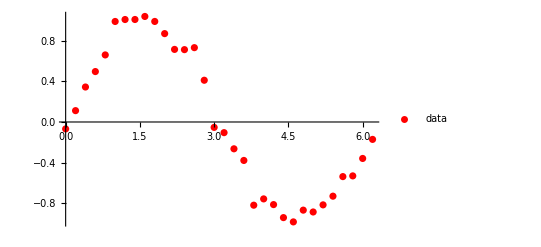

```mathematica
data=Table[
{x,Sin@x+.1RandomVariate[NormalDistribution[]]},
{x,0,2π,.2}];
ListPlot[data,PlotStyle->Red,PlotLegends->{"data"}]
```

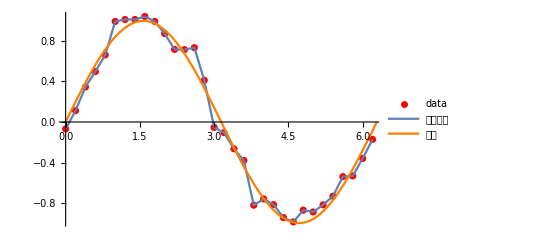

```mathematica
fit=NonlinearModelFit[data,A Sin[k x],{A,k},x];
Show[
ListPlot[data,PlotStyle->Red,PlotLegends->{"data"}],
ListLinePlot[data,PlotLegends->{"一阶插值"}],
Plot[fit@x,{x,0,2π},PlotStyle->Orange,PlotLegends->{"拟合"}]
]
```

插值多项式

过 3 个点的插值多项式：

```mathematica
InterpolatingPolynomial[{{0,1},{1,3},{3,2}},x]
```

1+(2-5/6 (-1+x)) x

简化用法：不给横坐标，默认是正整数序列

```mathematica
poly=InterpolatingPolynomial[{4,7,2,8,9},x]
```

4+(3+(-4+(19/6-35/24 (-4+x)) (-3+x)) (-2+x)) (-1+x)

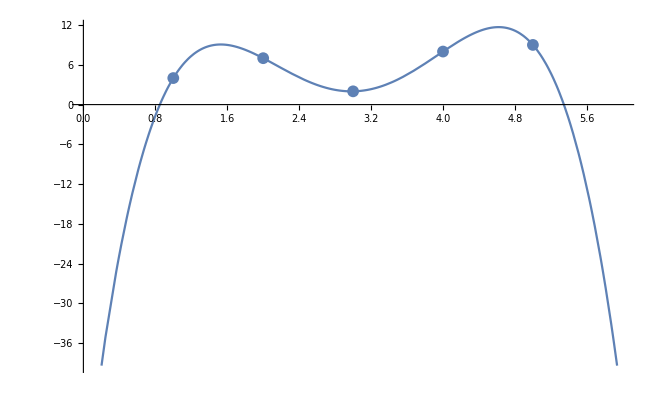

```mathematica
Show[Plot[poly,{x,0,6}],ListPlot[{4,7,2,8,9}]]
```

一般来说，n 个给定点可以确定一个 n-1 次插值多项式。（也有「巧了」的特殊情况；额外指定导数的情形更复杂）

小技巧：InterpolatingPolynomial 不只可以用来做数值计算，也可做符号计算。可用于公式推导（比如数值分析领域）。

```mathematica
InterpolatingPolynomial[{{Subscript[x, 1],a},{Subscript[x, 2],b},{Subscript[x, 3],c}},x]
```

a+(x-x_1) ((-a+b)/(-x_1+x_2)+((x-x_2) (-(-a+b)/(-x_1+x_2)+(-b+c)/(-x_2+x_3)))/(-x_1+x_3))

多元函数、指定导数的用法，参见帮助文档。

插值多项式一般用于理论推导用途，或者数据量很小时。
数据较多时（比如 100 个数据点，插值得 99 次多项式），面临两个问题：
1. 计算成本较高
2. 振荡问题（Runge 龙格现象）

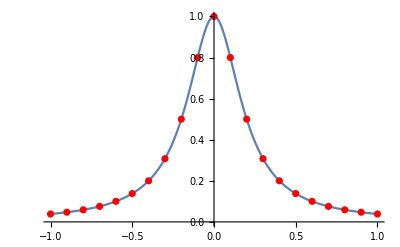

```mathematica
f[x_]:=1/(1+25 x^2);
data=Table[{x,f@x},{x,-1,1,.1}];
Show[
Plot[f@x,{x,-1,1}],
ListPlot[data,PlotStyle->Red]
]
```

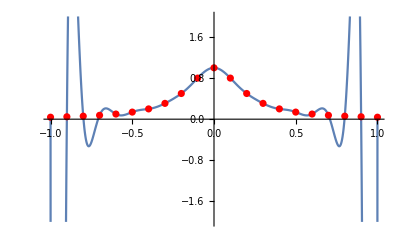

```mathematica
poly=InterpolatingPolynomial[data,x];
Show[
Plot[poly,{x,-1,1},PlotRange->2],
ListPlot[data,PlotStyle->Red]
]
```

如何更「顺滑」地连接这些点？
用「分段插值」

构建插值函数

## Interpolation 内插

Interpolation 构建一个 InterpolatingFunction 对象，可以当做正常的函数调用。

```mathematica
f[x_]:=1/(1+25 x^2);
data=Table[{x,f@x},{x,-1,1,.1}];
ifun=Interpolation[data]
```

InterpolatingFunction[…]

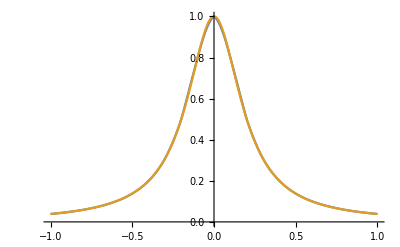

```mathematica
Plot[{ifun@x,f@x},{x,-1,1}]
```

参见帮助文档：
更多语法
多元函数的插值
InterpolationOrder
PeriodicInterpolation

## ListInterpolation 规则数组的插值

适用于坐标处于「规则网格」上的情形
输入函数值组成的规则数组，然后单独指定坐标范围。

## FunctionInterpolation 函数插值

用于把给定函数（可能是黑箱）自动采样，并进行插值
一维情况下有自适应采样，高维貌似没有

理解 InterpolatingFunction

InterpolatingFunction 是一个「对象」，它把底层的分段函数隐藏到了黑箱里，只展露出一个简洁紧凑的面板。
面板上展示了这个插值函数的基本属性：缩略图、定义域、输出形式、插值阶数、插值方法、周期性

```mathematica
f[x_]:=1/(1+25 x^2);
data=Table[{x,f@x},{x,-1,1,.1}];
ifun=Interpolation[data]
```

InterpolatingFunction[…]

首先，它可以当普通函数使用：求值

```mathematica
ifun[0]
```

1.

作用于某个未知变量时，原样返回，不把底层的分段函数暴露出来。不过这并不意味着计算失败，仍然可以用来画图、进一步赋值

InterpolatingFunction[…][x]

1.

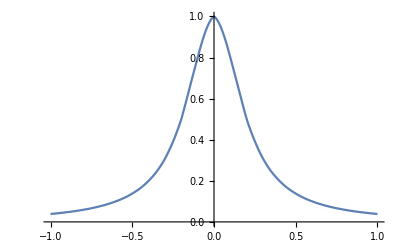

```mathematica
ifun[x]
ifun[x]/.x->0
Plot[ifun@x,{x,-1,1}]
```

可以直接求导
注意求导会降低插值阶数，变得不那么光滑

```mathematica
D[ifun@x,x]
ifun'
```

InterpolatingFunction[…][x]

InterpolatingFunction[…]

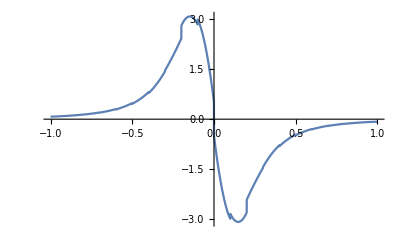

```mathematica
Plot[ifun'[x],{x,-1,1}]
```

可以直接定积分、不定积分

```mathematica
Integrate[ifun[x],{x,-1,1}]
Integrate[f[x],{x,-1,1}]//N
```

0.549373

0.54936

```mathematica
Integrate[ifun@x,x]
Derivative[-1][ifun]
```

InterpolatingFunction[…][x]

InterpolatingFunction[…][#1]&

通过「关键字」可以提取其属性
输入“Methods” 关键字：查看都有哪些关键字

```mathematica
ifun["Methods"]
```

{Coordinates,DerivativeOrder,Domain,ElementMesh,Evaluate,GetPolynomial,Grid,InterpolationMethod,InterpolationOrder,MethodInformation,Methods,OutputDimensions,Periodicity,PlottableQ,Properties,QuantityUnits,Unpack,ValuesOnGrid}

常用的几个关键字：

```mathematica
ifun@"Coordinates"
```

{{-1.,-0.9,-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}}

```mathematica
ifun@"ValuesOnGrid"
```

{0.0384615,0.0470588,0.0588235,0.0754717,0.1,0.137931,0.2,0.307692,0.5,0.8,1.,0.8,0.5,0.307692,0.2,0.137931,0.1,0.0754717,0.0588235,0.0470588,0.0384615}

有一个自我描述的关键字：“MethodInformation”
这里不多介绍，将来在进阶课程里面探索。

```mathematica
ifun["MethodInformation"["Grid"]]
```

System`InterpolatingFunction`Grid

InterpolatingFunction[domain, data]@Grid[] gives the grid of points where the interpolated data is defined.

Attributes[System`InterpolatingFunction`Grid]={Protected}
 
Options[System`InterpolatingFunction`Grid]={DropPeriodicEndpoint→False}

## 线性代数

2022-08-06

参见：guide/MatricesAndLinearAlgebra
思维导图：
-Graphics-

绪论

本节课只讨论「具体的」有限维线性代数。
Mathematica 支持「抽象的」张量代数的简单运算，但比较高级，入门教程暂不讨论。
Mathematica 同时有数值计算和符号计算能力，纯数值计算可能不如 MATLAB ，但符号计算能力是优势。

## 矢量的表示（回顾）

矢量可以由 单层列表 List 表示

```mathematica
{1,2,3}+{a,b,c}
```

{1+a,2+b,3+c}

矩阵

## 矩阵的表示

用二维的数组（「规则的」列表）表示矩阵：

```mathematica
{{a,b},{c,d}}
```

{{a,b},{c,d}}

显示为矩阵形式：

```mathematica
{{a,b},{c,d}}//MatrixForm
```

(a | b
c | d)

```mathematica
{{a,b},
{c,d}}
```

二维输入（快捷、直观）：

```mathematica
({{a, b}, {c, d}})
```

{{a,b},{c,d}}

行向量、列向量是矩阵的特殊形式。

```mathematica
{{1,2}}//MatrixForm
{{1},{2}}//MatrixForm
```

(1 | 2)

(1
2)

实际上，个人觉得统一使用单层列表 {1,2} 表示向量就好，这种写法推广到张量更方便。两种不同写法能做到的事情是一致的，只是列表层级有区别。

```mathematica
({{a, b}, {c, d}}).{1,2}
({{a, b}, {c, d}}).({{1}, {2}})
```

{a+2 b,c+2 d}

{{a+2 b},{c+2 d}}

```mathematica
{1,2}.({{a, b}, {c, d}})
({{1, 2}}).({{a, b}, {c, d}})
```

{a+2 c,b+2 d}

{{a+2 c,b+2 d}}

```mathematica
{1,2}.({{a, b}, {c, d}}).{3,4}
({{1, 2}}).({{a, b}, {c, d}}).({{3}, {4}})
```

3 (a+2 c)+4 (b+2 d)

{{3 (a+2 c)+4 (b+2 d)}}

```mathematica
ConjugateTranspose@{1,2I}
ConjugateTranspose@({{1}, {2I}})
```

{1,-2 ⅈ}

{{1,-2 ⅈ}}

## 构造矩阵

## 用 Table 或 Array 生成矩阵

```mathematica
Table[Subscript[a, i,j],{i,1,3},{j,1,3}]//MatrixForm
Table[i+j,{i,1,3},{j,1,3}]//MatrixForm
```

(a_(1,1) | a_(1,2) | a_(1,3)
a_(2,1) | a_(2,2) | a_(2,3)
a_(3,1) | a_(3,2) | a_(3,3))

(2 | 3 | 4
3 | 4 | 5
4 | 5 | 6)

```mathematica
Array[a,{3,3}]//MatrixForm
Array[Subscript[a, ##]&,{3,3}]//MatrixForm
```

(a[1,1] | a[1,2] | a[1,3]
a[2,1] | a[2,2] | a[2,3]
a[3,1] | a[3,2] | a[3,3])

(a_(1,1) | a_(1,2) | a_(1,3)
a_(2,1) | a_(2,2) | a_(2,3)
a_(3,1) | a_(3,2) | a_(3,3))

### SparseArray 稀疏数组

这个函数名叫「稀疏数组」，实际上是一种通过指定非零元的规律，高效表示数组（尤其是稀疏数组）的方式。

参见帮助文档 SparseArray

### 其他构造矩阵的方法

其他构造矩阵的方法，参见：guide/ConstructingMatrices

## 基本矩阵运算

### 转置 Transpose

使用 tr 打出转置符号ᵀ

```mathematica
Transpose@({{a, b}, {c, d}})
({{a, b}, {c, d}})ᵀ
```

{{a,c},{b,d}}

{{a,c},{b,d}}

转置的妙用：用于在 {{x1,y1},{x2,y2},{x3,y3},...} 和 {{x1,x2,x3,...},{y1,y2,y3,...}} 之间切换

```mathematica
{{1,2,3,4,5},{a,b,c,d,e}}ᵀ
```

{{1,a},{2,b},{3,c},{4,d},{5,e}}

### 矩阵乘法、向量内积 Dot

Dot 可以直接用 . 号（英文句号）简写
Dot 实际上有很广泛的用法，矩阵乘矩阵、矩阵乘向量、向量内积，本质上是张量缩并

```mathematica
Dot[({{a, b}, {c, d}}),({{1, 2}, {3, 4}})]
({{a, b}, {c, d}}).({{1, 2}, {3, 4}})
```

{{a+3 b,2 a+4 b},{c+3 d,2 c+4 d}}

{{a+3 b,2 a+4 b},{c+3 d,2 c+4 d}}

注意不要直接使用乘法（Times），那个是按元素相乘

```mathematica
({{a, b}, {c, d}})*({{1, 2}, {3, 4}})
```

{{a,2 b},{3 c,4 d}}

### 矩阵幂次 MatrixPower

```mathematica
MatrixPower[({{a, b}, {c, d}}),2]
({{a, b}, {c, d}}).({{a, b}, {c, d}})==%
```

{{a^2+b c,a b+b d},{a c+c d,b c+d^2}}

True

注意不要直接乘方！那个是每个矩阵元素的幂次

```mathematica
({{a, b}, {c, d}})^2
({{a, b}, {c, d}})^2
```

{{a^2,b^2},{c^2,d^2}}

{{a^2,b^2},{c^2,d^2}}

### 矩阵求逆 Inverse

```mathematica
Inverse@({{a, b}, {c, d}})
```

{{d/(-b c+a d),-b/(-b c+a d)},{-c/(-b c+a d),a/(-b c+a d)}}

### 行列式 Det、迹 Tr

这里的命名法没有用全称，注意区分 Tr（矩阵的迹）与 Trace（追踪运算过程）

```mathematica
Det@({{a, b}, {c, d}})
Tr@({{a, b}, {c, d}})
```

-b c+a d

a+d

求解线性系统

guide/LinearSystems

LinearSolve 用于求解线性方程组 m.x==b

```mathematica
LinearSolve[({{1, 2}, {3, 4}})]
```

LinearSolveFunction[…]

NullSpace 给出矩阵零空间的基（即齐次通解的基本解）

MatrixRank 求矩阵的秩

RowReduce 高斯消去法 行约化

线性最优化

guide/MatrixBasedMinimization

LeastSquares 求解最小二乘问题

特征方程

Eigenvalues 求特征值
Eigenvectors 求特征向量
Eigensystem 同时求特征值和特征向量

```mathematica
Eigensystem[({{a, b}, {c, d}})]=={Eigenvalues@({{a, b}, {c, d}}),Eigenvectors@({{a, b}, {c, d}})}
```

True

```mathematica
Eigenvalues@({{a, b}, {c, d}})
```

{1/2 (a+d-√(a^2+4 b c-2 a d+d^2)),1/2 (a+d+√(a^2+4 b c-2 a d+d^2))}

```mathematica
Eigenvectors@({{a, b}, {c, d}})
```

{{-(-a+d+√(a^2+4 b c-2 a d+d^2))/(2 c),1},{-(-a+d-√(a^2+4 b c-2 a d+d^2))/(2 c),1}}

Mathematica 线性代数 应用举例：

参见我的「线性代数 revisited」视频中的 notebook

## 微分方程

2022-08-15 ~ 2023-01-25

参见：guide/DifferentialEquations
思维导图：
-Graphics-

绪论

欢迎来到《符号和数值计算》中最重要、最庞大的一课

微分方程（主要是 ODE 和 PDE）在数学、物理等的各个领域都有着非常广泛的应用。学会用 MMA 解微分方程，你就可以轻松地研究力学、电磁学、传热学、光学、量子力学、相对论、宇宙学、恒星物理等各个领域中的各种各样的方程/模型，帮助你做理论推导和数值模拟。

本节课涉及前面讲的 微积分、矢量分析、插值函数、线性代数 的部分内容

微分方程：关于未知函数及其导数的方程。
F(u(x),u’(x),...,u^(n)(x))=0
这里未知函数又称因变量、待求函数等

求解微分方程：找到满足方程的 u(x) 表达式
数值求解：算出近似满足方程的 u(x) 数据点（并插值成函数）

## 微分方程的分类

## Mathematica 的强大、简洁、统一

尽管微分方程的种类纷繁复杂，而每一类型的数学理论、表达形式、符号算法、数值算法又各不相同，但 Mathematica 提供了一种极其优雅的解决方式。

强大：
对上述各种类型的方程，均有相应的符号算法、数值算法。这些算法大多很「智能」，有自适应步长/精度控制，也可手动深入调节。

简洁：
所有的对方程的分类、变换、数值算法、精度控制都自动完成，并被隐藏在底层，对用户只展现出简洁的输入和输出。

统一：
所有微分方程都统一使用 DSolve 和 NDSolve 求符号和数值解。语法高度统一，只需要学会最简单的，就一法通万法通。
以下先讲 DSolve 符号解，但对 NDSolve 数值解也通用。

DSolve 符号解

## 输入格式

最简单的输入格式：
DSolve[eqn,u,x]
为函数 u 求解微分方程 eqn，x 为自变量.

```mathematica
DSolve[y'[x]==y[x],y,x]
DSolve[y'[x]==y[x],y[x],x]
```

{{y→Function[{x},ⅇ^x C[1]]}}

{{y[x]→ⅇ^x C[1]}}

ODE 的边界条件/初始条件 以 u[0]==1,u’[3]==a 这类方式给出
PDE 的边界条件也可以用类似形式，或者使用:

```mathematica
DirichletCondition
NeumannValue
PeriodicBoundaryCondition
```

如果有多个方程/边界条件/多个因变函数/多个自变量：
统一用列表 List 将它们装在一起
DSolve[{eqn_1,eqn_2,...,cond_1,cond_(2,...)},{u_1,u_2,...},{x_1,x_2,...}]

```mathematica
DSolve[{x'[t]==v[t],v'[t]==-x[t],v'[0]==0},{x[t],v[t]},t]
```

{{v[t]→C[1] Cos[t],x[t]→C[1] Sin[t]}}

指定自变量的范围：{{x,x_min,x_max},...}
指定自变量属于几何区域：{x,y,...}∈reg
时间+空间变量：{t,0,100},{x,y,...}∈reg
我们将在帮助文档中看到各种例子

tips: 对于比较复杂的方程、边界条件、因变函数，我们可以把他们分别命名到一些变量上，这样让 NDSolve 语句简洁清晰。
eqn = xxxx;(*equation*)
ics = xxxx;(*initial conditions*)
bcs = xxxx;(*boundary conditions*)
funcs = xxxx;(*functions*)
reg = xxxx;(*region*)
NDSolve[{eqn,ics,bcs},funcs,{x,y,...}∈reg]

## 输出格式

### 输出格式解读

DSolve 返回一个两层嵌套的「规则列表」

```mathematica
DSolve[y'[x]==y[x],y,x]
```

{{y→Function[{x},ⅇ^x C[1]]}}

```mathematica
y[x]/.%
```

{ⅇ^x C[1]}

为什么要嵌套两层 {{}} 这么麻烦？是为了应对多解的情况。
外层列表装的是「多解」，内层列表装的是「多个因变函数」。

```mathematica
DSolve[x'[t]^2==x[t]^4,x[t],t]
```

{{x[t]→1/(-t-C[1])},{x[t]→1/(t-C[1])}}

```mathematica
x[t]/.%
```

{1/(-t-C[1]),1/(t-C[1])}

如何使用「规则列表」？用 /. (ReplaceAll)  应用该规则对表达式进行替换。

### DSolve vs DSolveValue：推荐用 DSolve

DSolve 返回「规则」，而 DSolveValue 只返回值
而且 DSolveValue 只返回多解中的一个解

```mathematica
DSolveValue[x'[t]^2==x[t]^4,x[t],t]
```

DSolveValue::dsvb: 方程有多个解分支，但是 DSolveValue 只返回一个. 使用 DSolve 获取所有解分支.

1/(-t-C[1])

```mathematica
Values@DSolve[x'[t]^2==x[t]^4,x[t],t]
```

{{1/(-t-C[1])},{1/(t-C[1])}}

建议：图省事有时可以用 DSolveValue，不过还是 DSolve 包含的信息更多。而且规则列表的形式更方便使用
对比如下：

{x→Function[{t},Sin[t]]}

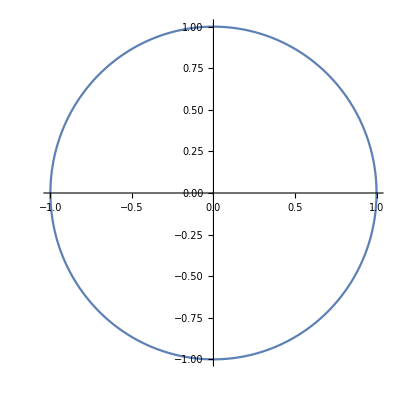

```mathematica
sol=DSolve[{x''[t]==-x[t],x[0]==0,x'[0]==1},x,t]//First
ParametricPlot[{x[t],x'[t]}/.sol,{t,0,2π}]
```

```mathematica
xsol=DSolveValue[{x''[t]==-x[t],x[0]==0,x'[0]==1},x,t]
ParametricPlot[{xsol[t],xsol'[t]},{t,0,2π}]
```

Function[{t},Sin[t]]

-Graphics-

### 返回 纯函数 u vs 表达式 u[x]：推荐「纯函数 u」

在 DSolve 的第二个 argument 处输入 {u_1,u_2,...} 而非{u_1[x],u_2[x],...} ，有许多好处

```mathematica
sol1=DSolve[{x''[t]==-x[t],x[0]==0,x'[0]==1},x,t]//First
sol2=DSolve[{x''[t]==-x[t],x[0]==0,x'[0]==1},x[t],t]//First
```

{x→Function[{t},Sin[t]]}

{x[t]→Sin[t]}

后者只能替换 x[t] 整个表达式，而前者能替换所有的 x，所以可以直接得到导数等

```mathematica
x[t]/.{sol1,sol2}
x[3]/.{sol1,sol2}
x'[t]/.{sol1,sol2}
```

{Sin[t],Sin[t]}

{Sin[3],x[3]}

{Cos[t],x'[t]}

## 更多语法、范例、应用， 让我们一起来看 DSolve 的帮助文档

帮助文档非常重要！！！学 Mathematica 一定要学会看帮助文档。比如 DSolve 的文档就非常详尽，不仅可以学到这个函数的用法，还可以学到如何使用微分方程的解、如何可视化、相关数学知识（很多是超出我们知识范畴的）、物理知识等等。

NDSolve 数值解

尽管 DSolve 很强大，但数学上大多数的微分方程（尤其是 PDE）都是没有解析解的。即使有级数解，在应用上也并不方便。

这时，我们就需要进行数值求解。 MMA 的统一性设计使得数值解使用起来几乎和符号解一样方便，例如在绘图、求导、积分、求零点、求极值点等方面。

NDSolve 的输入输出语法与 DSolve 几乎完全相同。
区别：
1. NDSolve 必须数值地给出全部定解条件（系数、边界条件等）以及自变量取值范围（例如 t_min、t_max），不能留着一些符号系数、未知项，否则无法解出数值解。
2. NDSolve 返回的是 InterpolatingFunction 插值函数。

仅此而已。

具体的范例、应用，
让我们一起来看 NDSolve 的帮助文档

如果你觉得这很平常，这是因为你已经被 MMA 的强大、简洁、统一给惯坏了。

如果是 MATLAB：
	自己从 ode45、ode113、ode23s、dde23、pdepe…… 中挑选合适的求解器
	自己把方程显化、改写为一阶方程组，并把因变函数归入一个向量的各分量
	对偏微分方程的支持较弱，只限于一些简单情况，复杂的需要自己写数值算法

微分特征值问题

还记得求解矩阵特征值问题的函数：Eigensystem 吗？
按照 MMA 统一的命名法，微分特征值问题当然就是 
DEigensystem & NDEigensystem

求解如下问题：
ℒ[u_i[x,y,…]]==λ_i u_i[x,y,…]

## DEigensystem 符号解

DEigensystem 的语法与 DSolve 有点像，不同之处在于：
1. 第一个 argument 是「线性微分算子」ℒ
	1.1 必须是线性，因为特征值问题就是对于线性算子的
	1.2 这里「微分算子」不只是求导（Laplacian 之类的），还包括（齐次）边界条件
2. 第四个 argument 要填待求的特征值个数 n
	2.1 很遗憾，DEigensystem 只能给出前 n 个特征值，不能给出通式
	2.2 想要通式用 DSolve

## NDEigensystem 数值计算

NDEigensystem 的语法与 DEigensystem 几乎完全相同
数值解没那么精确，但可以解决更多没有解析解的问题。

具体的范例、应用，
让我们一起来看 帮助文档

其他微分方程相关函数

WhenEvent 处理微分方程中的事件（比如碰撞、条件的突变）
GreenFunction 解析求解格林函数
CompleteIntegral 求一阶偏微分方程的全积分
DSolveChangeVariables 进行微分换元（链式法则），13.1版本引入

初始化单元

新手注意：
在本文档中，按「单元组」指定 Context，因此一个单元组之外的符号定义是不共享的，与其他笔记本之间也不共享。
这样的 Behavior 与 MMA 文档类似，而和通常的笔记本不同。通常自己写的笔记本，都是全局变量。

```mathematica
SetOptions[EvaluationNotebook[],CellContext->CellGroup]
```